## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

```mathematica
nCollatz[61]
```

{61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

## Topic

### Definition / Theorem

This is text.

#### Example

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,101,111}]//tf
```

101 | 5/2
102 | -1/51
103 | 1/51
104 | -2/13
105 | 2/13
106 | -1/53
107 | 1/53
108 | -1/18
109 | 1/18
110 | -1/55
111 | 1/55

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

```mathematica
nQuotientToNatural[4/5]
nQuotientToNatural[3/5]
nQuotientToNatural[7/25]
nQuotientToNatural[24/25]
nQuotientToNatural[-44/125]
nQuotientToNatural[117/125]
nQuotientToNatural[-527/625]
nQuotientToNatural[336/625]
nQuotientToNatural[-3116/3125]
nQuotientToNatural[-237/3125]

(4/5+3/5I)^5
```

161

91

12251

144001

12100000

85556251

43395156250

17640000001

37927562500000

219410156250

-3116/3125-(237 ⅈ)/3125

```mathematica
nQuotientToNatural[5/11]
FactorInteger[551]
nIntegerToNatural[19]
```

551

{{19,1},{29,1}}

39

```mathematica
nQuotientToNatural[7/13]
FactorInteger[1275]
nIntegerToNatural[3]
nIntegerToNatural[25]
nIntegerToNatural[17]
```

1275

{{3,1},{5,2},{17,1}}

7

51

35

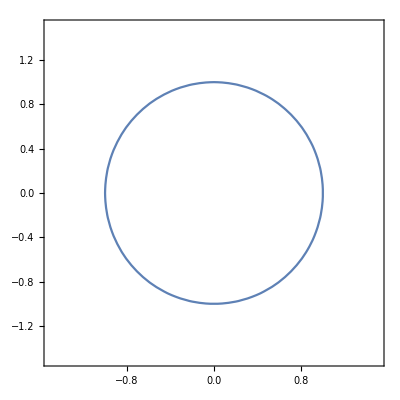

```mathematica
ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},AspectRatio->Automatic]
```

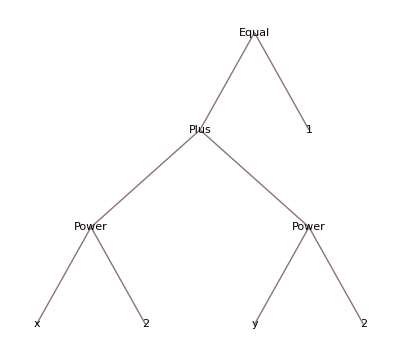

```mathematica
TreeForm[x^2+y^2==1]
```

## COUNTING

## ( 1 ) BASIC COUNTING

### Factorial

```mathematica
(* Definition Factorial Function *)
factorial[n_]:=1 /;n==0
factorial[n_]:=Product[k,{k,1,n}] /;n>0
factorial[10]
(* MMa Built-in *)
Factorial[10]
```

3628800

3628800

### Binomial Coefficient

```mathematica
(* Definition Binomial Coefficient *)
binomial[n_,k_]:=factorial[n]/(factorial[k]factorial[n-k])/;n>=0&&k>=0
binomial[6,3]
(* MMa Built-in *)
Binomial[6,3]
```

20

20

### Multinomial Coefficient

```mathematica
Multinomial[Sequence@@#]&/@Reverse[FrobeniusSolve[ConstantArray[1,1,2]]
```

```mathematica
(x+y+z)^3//Expand//FullForm;
(x+y+z)^3//Expand//Length;
(x+y+z)^3//Expand;
Binomial[5,3];
Multinomial[3,0,0];
Multinomial@@@Reverse[FrobeniusSolve[ConstantArray[1,3],3]];
FrobeniusSolve[Array[1&,3],3]//Reverse//TableForm;
Multinomial[Sequence@@#]&/@Reverse[FrobeniusSolve[ConstantArray[1,3],3]];
```

```mathematica
(x+y+z)^2//Expand//Length
(x+y+z)^2//Expand
Total[Flatten[CoefficientList[Expand[(x+y+z)^2],{x,y,z}]]]
```

6

x^2+2 x y+y^2+2 x z+2 y z+z^2

9

```mathematica
(x+y+z)^4//Expand
sum=Sum[KroneckerDelta[4-(n1+n2+n3)] Multinomial[n1,n2,n3] x^n1 y^n2 z^n3,{n1,0,4},{n2,0,4},{n3,0,4}]
```

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4

### Anagram Sets

### Types of Braces

### Definitions of Combinatorial Objects

### Words

### Permutations of A

### Partial Permutations

### Anagrams

### Sets

### Multisets

### Functions

### Injections

### Surjections

### Bijections

### Compositions of k

### Lattice Paths

### Dyck Paths

### Basic Counting Rules

### Probability Definitions